```mathematica
(1/(80*365))/((1/(80*365))+1/7)
```

7/29207

```mathematica
S=(1/R)-(2p/((R-1)+√((R-1)^2+4*R*p)))
```

1/R-(2 p)/(-1+R+√((-1+R)^2+4 p R))

```mathematica
V=(ϵ*(R-1)+ϵ*√((R-1)^2+4*R*p))/(2*R)
```

((7 (-1+R))/29207+(7 √((-1+R)^2+4 p R))/29207)/(2 R)

```mathematica
ϵ=7/29207
```

7/29207

```mathematica
Solve[(1-R S+R V+ϵ)^2-4 (R V+ϵ-R S ϵ)==0,p]
```

{{p→1/(182097552388294404 R^2)(-348642790720000 R+392442551314002 R^2-43622148233601 R^3-40 √29849554 √(-662110973845018574600 R^2+1988557208119318809807 R^3-1990783781830770850800 R^4+664337548214705880000 R^5))},{p→1/(182097552388294404 R^2)(-348642790720000 R+392442551314002 R^2-43622148233601 R^3+40 √29849554 √(-662110973845018574600 R^2+1988557208119318809807 R^3-1990783781830770850800 R^4+664337548214705880000 R^5))}}

```mathematica
Clear[p]
```

```mathematica
g[R_]:=1/(182097552388294404 R^2)(-348642790720000 R+392442551314002 R^2-43622148233601 R^3+40 √29849554 √(-662110973845018574600 R^2+1988557208119318809807 R^3-1990783781830770850800 R^4+664337548214705880000 R^5))
```

```mathematica
h[R_]:=g[R-1]
```

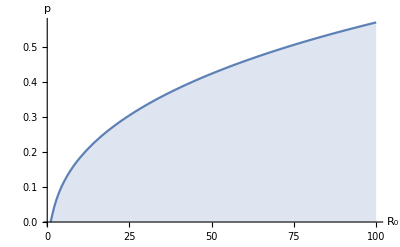

```mathematica
Plot[g[R],{R,0,100},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->All]
```

LogLinearPlot::invpr: Value of option PlotRange should be positive in the scaled dimensions.

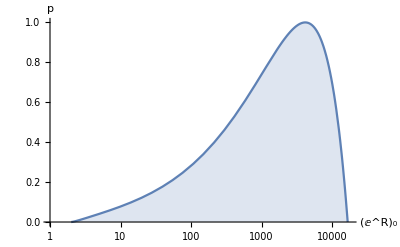

```mathematica
LogLinearPlot[h[R],{R,0.001,18000},Filling->Bottom,AxesLabel->{Subscript[R, 0],p},PlotRange->{{0,18000},{0,1}}]
```

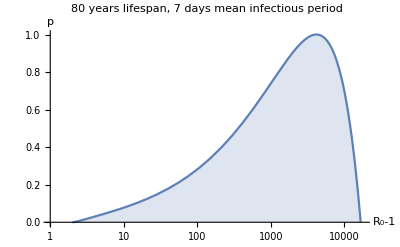

```mathematica
Show[%72,AxesLabel->{HoldForm[Subscript[R, 0]-1],p},PlotLabel->RawBoxes[RowBox[{RowBox[{"80"," ","years"," ","lifespan"}],","," ",RowBox[{"7"," ","days"," ","mean"," ","infectious"," ","period"}]}]],LabelStyle->{GrayLevel[0]}]
```